```mathematica
(*PacletInstall["EcoEvo","Site"->"http://raw.githubusercontent.com/cklausme/EcoEvo/master"]*)
```

```mathematica
Paclet["EcoEvo","1.7.1",<>]
```

PacletManager`Paclet[Name→EcoEvo,Version→1.7.1,MathematicaVersion→10+,Description→Species- and trait-based ecological and eco-evolutionary modeling.,Creator→Christopher Klausmeier <christopher.klausmeier@gmail.com>,Thumbnail→Logo.png,Root→EcoEvo,Icon→Logo.png,Extensions→{{Documentation,MainPage→Guides/EcoEvo,Language→All},{Kernel,Root→.,Context→EcoEvo`}},Location→/home/dipanjana/.Mathematica/Paclets/Repository/EcoEvo-1.7.1]

```mathematica
Needs["EcoEvo`"];
```

t::shdw: Symbol t appears in multiple contexts {EcoEvo`,Global`}; definitions in context EcoEvo` may shadow or be shadowed by other definitions.

```mathematica
SetModel[{
Pop[H1]->{Equation :> H1*(1-H1-H2) -  sp*H1*(sp *H1 + snp *H2 )^z *PA-snp*H1*(snp * H1 + sp * H2)^z * PB, Color-> Blue},
Pop[H2]->{Equation :> H2*(1-H1-H2) -  snp*H2*(sp *H1 + snp *H2 )^z *PA- sp*H2*(snp * H1 + sp * H2)^z * PB, Color-> Green},
Pop[PA] ->{Equation:>f*(sp * H1 + snp *H2)^(z+1)*PA -d*PA, Color -> Red},
Pop[PB] ->{Equation:>f*(snp * H1 + sp *H2)^(z+1)*PB -d*PB, Color -> Pink},
Parameters :> {sp >0, snp >=0, z !=-1, f>0, d>0}}];
```

```mathematica
L1 = 1/2 (-d+((d/f)^(1/(1+z)))^(1+z) f-((snp-sp)^2 (-2 (d/f)^(1/(1+z))+snp+sp) z)/(snp+sp)^3-1/(snp+sp)^3((d/f)^(1/(1+z)))^-z √(((d/f)^(1/(1+z)))^(2 z) (4 (2 (d/f)^(1/(1+z))-snp-sp) (snp-sp)^2 (snp+sp)^3 (((d/f)^(1/(1+z)))^(1+z) f+d z)+(-d (snp+sp)^3+((d/f)^(1/(1+z)))^(1+z) f (snp+sp)^3+(2 (d/f)^(1/(1+z))-snp-sp) (snp-sp)^2 z)^2)));
L2 = 1/2 (-d+((d/f)^(1/(1+z)))^(1+z) f-((snp-sp)^2 (-2 (d/f)^(1/(1+z))+snp+sp) z)/(snp+sp)^3+1/(snp+sp)^3((d/f)^(1/(1+z)))^-z √(((d/f)^(1/(1+z)))^(2 z) (4 (2 (d/f)^(1/(1+z))-snp-sp) (snp-sp)^2 (snp+sp)^3 (((d/f)^(1/(1+z)))^(1+z) f+d z)+(-d (snp+sp)^3+((d/f)^(1/(1+z)))^(1+z) f (snp+sp)^3+(2 (d/f)^(1/(1+z))-snp-sp) (snp-sp)^2 z)^2)));
L3 = 1/2 (-d+((d/f)^(1/(1+z)))^(1+z) f-1/(snp+sp)(-2 (d/f)^(1/(1+z)) (-1+z)+(snp+sp) z+((d/f)^(1/(1+z)))^-z √(((d/f)^(1/(1+z)))^(2 z) ((snp+sp)^2 (d-z)^2+(d/f)^(2/(1+z)) (((d/f)^(1/(1+z)))^(2 z) f^2 (snp+sp)^2+4 (-1+z)^2+4 ((d/f)^(1/(1+z)))^z f (snp+sp) (3+z))-2 (d/f)^(1/(1+z)) (snp+sp) (-2 (d-z) (-1+z)+((d/f)^(1/(1+z)))^z f (snp+sp) (2+d+z))))));
L4 = 1/2 (-d+((d/f)^(1/(1+z)))^(1+z) f+1/(snp+sp)(2 (d/f)^(1/(1+z)) (-1+z)-(snp+sp) z+((d/f)^(1/(1+z)))^-z √(((d/f)^(1/(1+z)))^(2 z) ((snp+sp)^2 (d-z)^2+(d/f)^(2/(1+z)) (((d/f)^(1/(1+z)))^(2 z) f^2 (snp+sp)^2+4 (-1+z)^2+4 ((d/f)^(1/(1+z)))^z f (snp+sp) (3+z))-2 (d/f)^(1/(1+z)) (snp+sp) (-2 (d-z) (-1+z)+((d/f)^(1/(1+z)))^z f (snp+sp) (2+d+z))))));
```

case1: snp = 0, plots for z = 0, z=0.05, and 0.5

```mathematica
sp = 0.5;
f=1;
d=0.1;
```

```mathematica
sp+0>2(d/f)^(1/(1+zz))
```

0.5>2 0.1^(1/(1+zz))

```mathematica
Solve[sp==2(d/f)^(1/(1+zz)),zz]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{zz→0.660964}}

```mathematica
Manipulate[Plot[Max[{Re[1/2 (-d+((d/f)^(1/(1+z)))^(1+z) f-((snp-sp)^2 (-2 (d/f)^(1/(1+z))+snp+sp) z)/(snp+sp)^3-1/(snp+sp)^3((d/f)^(1/(1+z)))^-z √(((d/f)^(1/(1+z)))^(2 z) (4 (2 (d/f)^(1/(1+z))-snp-sp) (snp-sp)^2 (snp+sp)^3 (((d/f)^(1/(1+z)))^(1+z) f+d z)+(-d (snp+sp)^3+((d/f)^(1/(1+z)))^(1+z) f (snp+sp)^3+(2 (d/f)^(1/(1+z))-snp-sp) (snp-sp)^2 z)^2)))],Re[1/2 (-d+((d/f)^(1/(1+z)))^(1+z) f-((snp-sp)^2 (-2 (d/f)^(1/(1+z))+snp+sp) z)/(snp+sp)^3+1/(snp+sp)^3((d/f)^(1/(1+z)))^-z √(((d/f)^(1/(1+z)))^(2 z) (4 (2 (d/f)^(1/(1+z))-snp-sp) (snp-sp)^2 (snp+sp)^3 (((d/f)^(1/(1+z)))^(1+z) f+d z)+(-d (snp+sp)^3+((d/f)^(1/(1+z)))^(1+z) f (snp+sp)^3+(2 (d/f)^(1/(1+z))-snp-sp) (snp-sp)^2 z)^2)))],Re[1/2 (-d+((d/f)^(1/(1+z)))^(1+z) f-1/(snp+sp)(-2 (d/f)^(1/(1+z)) (-1+z)+(snp+sp) z+((d/f)^(1/(1+z)))^-z √(((d/f)^(1/(1+z)))^(2 z) ((snp+sp)^2 (d-z)^2+(d/f)^(2/(1+z)) (((d/f)^(1/(1+z)))^(2 z) f^2 (snp+sp)^2+4 (-1+z)^2+4 ((d/f)^(1/(1+z)))^z f (snp+sp) (3+z))-2 (d/f)^(1/(1+z)) (snp+sp) (-2 (d-z) (-1+z)+((d/f)^(1/(1+z)))^z f (snp+sp) (2+d+z))))))], Re[1/2 (-d+((d/f)^(1/(1+z)))^(1+z) f+1/(snp+sp)(2 (d/f)^(1/(1+z)) (-1+z)-(snp+sp) z+((d/f)^(1/(1+z)))^-z √(((d/f)^(1/(1+z)))^(2 z) ((snp+sp)^2 (d-z)^2+(d/f)^(2/(1+z)) (((d/f)^(1/(1+z)))^(2 z) f^2 (snp+sp)^2+4 (-1+z)^2+4 ((d/f)^(1/(1+z)))^z f (snp+sp) (3+z))-2 (d/f)^(1/(1+z)) (snp+sp) (-2 (d-z) (-1+z)+((d/f)^(1/(1+z)))^z f (snp+sp) (2+d+z))))))]}],{z, 0.00, 0.5},PlotRange-> {-0.2, 0.2}, AxesLabel ->{"z", "eigenvalues"} , PlotLegends->{Placed["Eigenvalues w.r.t functional response",Top]}] ,{f,{1}},{sp,0.5,1},{snp,{0,0.05, 0.5}},{d,{0.1}}]
```

Pick::incomp: Expressions {{{Atoms,atoms,{element colors,Jmol colors,CPK colors}},{Named},1,{H,He,Li,Be,B,C,N,O,F,Ne,«108»},{color,color,color,color,color,color,color,color,color,color,«108»},{1,2,3,4,5,6,7,8,9,10,«108»},None,These colors are used to distinguish elements in illustrations and graphics, such as molecule plot. It is based on Corey, Pauling, Kultin color scheme.},«9»,«247»} and {Atoms,Crayola,GeologicAges,HTML,Legacy,WebSafe,1,2,3,4,«248»} have incompatible shapes.

ColorData::notprop: ColorList is not a known property for ColorData. Use ColorData["Properties"] for a list of properties.

```mathematica
Manipulate[Plot[Max[{Re[1/2 (-d+((d/f)^(1/(1+z)))^(1+z) f-((snp-sp)^2 (-2 (d/f)^(1/(1+z))+snp+sp) z)/(snp+sp)^3-1/(snp+sp)^3((d/f)^(1/(1+z)))^-z √(((d/f)^(1/(1+z)))^(2 z) (4 (2 (d/f)^(1/(1+z))-snp-sp) (snp-sp)^2 (snp+sp)^3 (((d/f)^(1/(1+z)))^(1+z) f+d z)+(-d (snp+sp)^3+((d/f)^(1/(1+z)))^(1+z) f (snp+sp)^3+(2 (d/f)^(1/(1+z))-snp-sp) (snp-sp)^2 z)^2)))],Re[1/2 (-d+((d/f)^(1/(1+z)))^(1+z) f-((snp-sp)^2 (-2 (d/f)^(1/(1+z))+snp+sp) z)/(snp+sp)^3+1/(snp+sp)^3((d/f)^(1/(1+z)))^-z √(((d/f)^(1/(1+z)))^(2 z) (4 (2 (d/f)^(1/(1+z))-snp-sp) (snp-sp)^2 (snp+sp)^3 (((d/f)^(1/(1+z)))^(1+z) f+d z)+(-d (snp+sp)^3+((d/f)^(1/(1+z)))^(1+z) f (snp+sp)^3+(2 (d/f)^(1/(1+z))-snp-sp) (snp-sp)^2 z)^2)))],Re[1/2 (-d+((d/f)^(1/(1+z)))^(1+z) f-1/(snp+sp)(-2 (d/f)^(1/(1+z)) (-1+z)+(snp+sp) z+((d/f)^(1/(1+z)))^-z √(((d/f)^(1/(1+z)))^(2 z) ((snp+sp)^2 (d-z)^2+(d/f)^(2/(1+z)) (((d/f)^(1/(1+z)))^(2 z) f^2 (snp+sp)^2+4 (-1+z)^2+4 ((d/f)^(1/(1+z)))^z f (snp+sp) (3+z))-2 (d/f)^(1/(1+z)) (snp+sp) (-2 (d-z) (-1+z)+((d/f)^(1/(1+z)))^z f (snp+sp) (2+d+z))))))], Re[1/2 (-d+((d/f)^(1/(1+z)))^(1+z) f+1/(snp+sp)(2 (d/f)^(1/(1+z)) (-1+z)-(snp+sp) z+((d/f)^(1/(1+z)))^-z √(((d/f)^(1/(1+z)))^(2 z) ((snp+sp)^2 (d-z)^2+(d/f)^(2/(1+z)) (((d/f)^(1/(1+z)))^(2 z) f^2 (snp+sp)^2+4 (-1+z)^2+4 ((d/f)^(1/(1+z)))^z f (snp+sp) (3+z))-2 (d/f)^(1/(1+z)) (snp+sp) (-2 (d-z) (-1+z)+((d/f)^(1/(1+z)))^z f (snp+sp) (2+d+z))))))]}],{snp,0, 0.5},PlotRange-> {-0.2, 0.2}, AxesLabel ->{"σ_np", "eigenvalues"} , (*Epilog->{Gray, Opacity[0.2],Rectangle[{2(d/f)^(1/(1+z))-sp, -800},{sp,800}]},*)PlotLegends->{Placed["Eigenvalues w.r.t scaled non-preferred susceptibility",Top]}],{f,{1}},{sp,0.5,1},{z,{0,0.05, 0.5}},{d,{0.1}}] (*for d = 0.1, f=1, and z = 0, sp+snp needs to be 0.2 min*)
```

Pick::incomp: Expressions {{{Atoms,atoms,{element colors,Jmol colors,CPK colors}},{Named},1,{H,He,Li,Be,B,C,N,O,F,Ne,«108»},{color,color,color,color,color,color,color,color,color,color,«108»},{1,2,3,4,5,6,7,8,9,10,«108»},None,These colors are used to distinguish elements in illustrations and graphics, such as molecule plot. It is based on Corey, Pauling, Kultin color scheme.},«9»,«247»} and {Atoms,Crayola,GeologicAges,HTML,Legacy,WebSafe,1,2,3,4,«248»} have incompatible shapes.

ColorData::notprop: ColorList is not a known property for ColorData. Use ColorData["Properties"] for a list of properties.

```mathematica
Equibbyhand={H1->(d/f)^(1/(1+z))/(snp+sp),H2->(d/f)^(1/(1+z))/(snp+sp),PA->(((d/f)^(1/(1+z)))^-z (-2 (d/f)^(1/(1+z))+snp+sp))/(snp+sp)^2,PB->(((d/f)^(1/(1+z)))^-z (-2 (d/f)^(1/(1+z))+snp+sp))/(snp+sp)^2};
```

```mathematica
Equibbyhand/.{sp=0.5, snp=0.0, d=0.1, f=1, z=0.5}
```

ReplaceAll::reps: {0.5,0.,0.1,1,0.5} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{H1→0.185981,H2→0.185981,PA→1.16803,PB→1.16803}/.{0.5,0.,0.1,1,0.5}

```mathematica
Manipulate[
sol = NDSolve[
{H1'[t]==H1[t](1-H1[t]-H2[t]) -sp H1[t](sp H1[t]  + snp H2[t])^z PA[t] -  snp H1[t](snp H1[t] + sp H2[t])^z PB[t], H1[0]==0.1, 
H2'[t]==H2[t](1-H1[t]-H2[t]) -snp H2[t](sp H1[t]  + snp H2[t])^z PA[t] - sp H2[t](snp H1[t] + sp H2[t])^z PB[t], H2[0] ==0.5,
PA'[t]==f (sp H1[t]  + snp H2[t])^(z+1) PA[t]    -d PA[t], PA[0]==0.01,
PB'[t]==f (snp H1[t]  + sp H2[t])^(z+1) PB[t]  -d PB[t], PB[0]==0.05}, {H1, H2, PA, PB},{t, 0, 1000}];Plot[{Evaluate[H1[t]/.sol],Evaluate[H2[t]/.sol],Evaluate[PA[t]/.sol],Evaluate[PB[t]/.sol]}, {t, 0, 1000},PlotStyle->{Blue, Green, Red, Pink}, PlotRange->All], {snp, {0, 0.0001,0.05,0.2, 0.5}},{f,1},{d,0.1},{z, {0, 0.0001,0.05, 0.5}},{sp, 0.5}]
```

```mathematica
Clear[sol, solve, sol1, sol2]
```

```mathematica
sol = NDSolve[
{H1'[t]==H1[t](1-H1[t]-H2[t]) -sp H1[t](sp H1[t]  + snp H2[t])^z PA[t] -  snp H1[t](snp H1[t] + sp H2[t])^z PB[t], H1[0]==0.1, 
H2'[t]==H2[t](1-H1[t]-H2[t]) -snp H2[t](sp H1[t]  + snp H2[t])^z PA[t] - sp H2[t](snp H1[t] + sp H2[t])^z PB[t], H2[0] ==0.5,
PA'[t]==f (sp H1[t]  + snp H2[t])^(z+1) PA[t]    -d PA[t], PA[0]==0.01,
PB'[t]==f (snp H1[t]  + sp H2[t])^(z+1) PB[t]  -d PB[t], PB[0]==0.05}, {H1, H2, PA, PB},{t, 0, 1000}];
```

```mathematica
sol[[1]]
```

{H1→InterpolatingFunction[{{0., 100000.}}, <>],H2→InterpolatingFunction[{{0., 100000.}}, <>],PA→InterpolatingFunction[{{0., 100000.}}, <>],PB→InterpolatingFunction[{{0., 100000.}}, <>]}

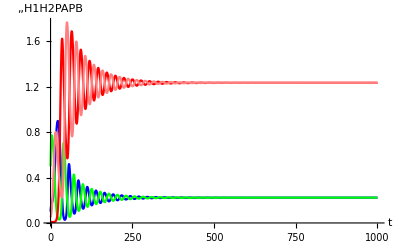

```mathematica
PlotDynamics[sol]
```

```mathematica
FinalSlice[[sol]]
```

Part::pkspec1: The expression {{H1 -> InterpolatingFunction[{{0., 100000.}}, <>], <<3>>}} cannot be used as a part specification.

FinalSlice⟦{{H1→InterpolatingFunction[{{0., 100000.}}, <>],H2→InterpolatingFunction[{{0., 100000.}}, <>],PA→InterpolatingFunction[{{0., 100000.}}, <>],PB→InterpolatingFunction[{{0., 100000.}}, <>]}}⟧